```mathematica
(*Conductivity according to BCS -- see https://journals.aps.org/pr/pdf/10.1103/PhysRev.111.412 or http://aip.scitation.org/doi/pdf/10.1063/1.324387*)
```

```mathematica
(*Definitions*)
e1[e_,Δ_]:=(e^2-Δ^2)^(1/2);
e2[e_,Δ_,hf_]:=((e+hf)^2-Δ^2)^(1/2);
e32[e_,Δ_,hf_]:=e^2+Δ^2+hf e;
e4[e_,Δ_]:=(Δ^2-e^2)^(1/2);
g[e_,Δ_,hf_]:=e32[e,Δ,hf]/(e1[e,Δ]×e2[e,Δ,hf]);

g2[e_,Δ_,hf_]:=e32[e,Δ,hf]/(e4[e,Δ]×e2[e,Δ,hf]);
fd[e_,kT_]:=(Exp[e/kT]+1)^-1;
ff[e_,hf_,kT_]:=fd[e,kT]-fd[e+hf,kT];
f2[e_,hf_,kT_]:=1-2fd[e+hf,kT];
int1[e_,Δ_,hf_,kT_]:=ff[e,hf,kT]×g[e,Δ,hf];
int11[e_,Δ_,hf_,kT_]:=f2[e,hf,kT]×g[e,Δ,hf];
int2[e_,Δ_,hf_,kT_]:=f2[e,hf,kT]×g2[e,Δ,hf];
```

```mathematica
(*Normalized real part conductivity*)
(*The real and imaginary part of normalized optical conductivity are given by;
σ1n[Δ_,hf_,kT_]:=2/hf∫_Δ^∞ int1[e,Δ,hf,kT]ⅆe+1/hf∫_(Δ-hf)^-Δ int11[e,Δ,hf,kT]ⅆe;
σ2n[Δ_,hf_,kT_]:=1/hf∫_(Δ-hf,-Δ)^Δ int2[e,Δ,hf,kT]ⅆe;
*)
(*To calculate this expression, the singularities are removed by changing the variables of integration;
See http://dspace.mit.edu/bitstream/handle/1721.1/61254/701906470-MIT.pdf;sequence=2*)
σ1nmenos[Δ_,hf_,kT_]:=2/hf NIntegrate[int1[Δ+x^2,Δ,hf,kT]2 x,{x,0,20 Δ^(1/2)}];
σ1nmas[Δ_,hf_,kT_]:=1/hf(NIntegrate[int11[Δ-hf+x^2,Δ,hf,kT]2 x,{x,0,√(hf/2-Δ)}]+
NIntegrate[int11[-Δ-x^2,Δ,hf,kT]2 x,{x,0,√(hf/2-Δ)}]);
σ1n[Δ_,hf_,kT_]:=
If[hf≤2Δ,
σ1nmenos[Δ,hf,kT],
σ1nmenos[Δ,hf,kT]-σ1nmas[Δ,hf,kT]
];

σ2nmenos[Δ_,hf_,kT_]:=1/hf(NIntegrate[int2[Δ-hf+x^2,Δ,hf,kT]2 x,{x,0,(1/2 hf)^(1/2)}]+NIntegrate[int2[Δ-x^2,Δ,hf,kT]2 x,{x,0,(1/2 hf)^(1/2)}]);
σ2nmas[Δ_,hf_,kT_]:=1/hf(NIntegrate[int2[-Δ+x^2,Δ,hf,kT]2 x,{x,0,Δ^(1/2)}]+NIntegrate[int2[Δ-x^2,Δ,hf,kT]2 x,{x,0,Δ^(1/2)}]);


σ2n[Δ_,hf_,kT_]:=
If[hf≤2Δ,
σ2nmenos[Δ,hf,kT],
σ2nmas[Δ,hf,kT]
];
```

0.0000861733

0.01

14

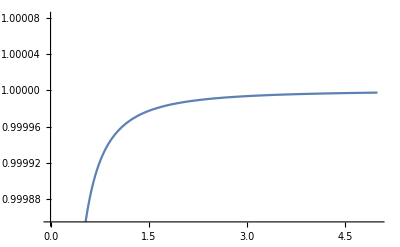

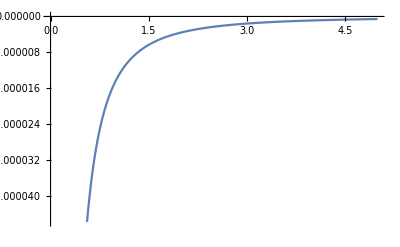

```mathematica
σn[Δ_,hf_,kT_]:=σ1n[Δ,hf,kT]-ⅈ σ2n[Δ,hf,kT];


(*Gap at T=0K, BCS theory*)
kB=8.6173303×10^-5
Δo[Tc_]:=1.764 kB Tc (*eV*);


Δ[T_,Tc_]:=Δo[Tc](Cos[π/2(T/Tc)^2 ])^(1/2);

(*Gap frequency*)
fgap[Δ_]:=2Δ/h




tempk = .01
tc = 14



Plot[Re[σn[Δ[tempk,tc],f,tempk]],{f,0,5}]
Plot[Im[σn[Δ[tempk,tc],f,tempk]],{f,0,5}]
```